```mathematica
SetDirectory[NotebookDirectory[]];
ImgFile=Import[".\\Images before baking\\01- Minimum spot.bmp"];
imgData=ImageData[ImgFile];
Dimensions[imgData]
```

{960,1280,3}

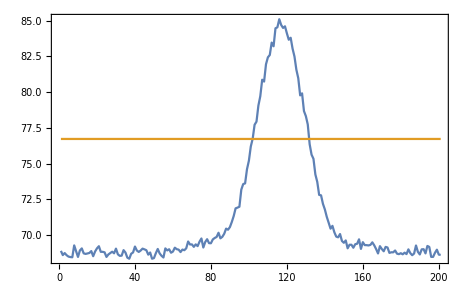

```mathematica
imgDataRow=Total[imgData⟦All,All,1⟧,{1}];
RowData=imgDataRow⟦600;;800⟧;
ListPlot[{RowData,Table[(Max[RowData]+Min[RowData])/2,Length[RowData]]},Joined->True,PlotRange->All,Frame->True]
```

```mathematica
(132-102)/12.
```

2.5

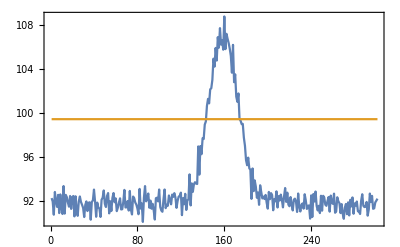

```mathematica
ImgFile=Import["C:\\Users\\Rb\\Pictures\\AkS- GRIN lens heat test\\Images before baking\\01- Minimum spot.bmp"];
imgData=ImageData[ImgFile];
imgDataCol=Total[imgData⟦All,All,1⟧,{2}];
ColData=imgDataCol⟦300;;600⟧;
ListPlot[{ColData,Table[(Max[ColData]+Min[ColData])/2,Length[ColData]]},Joined->True,PlotRange->All,Frame->True]
```

```mathematica
(175-143)/12.
```

2.66667